```mathematica
SetDirectory[NotebookDirectory[]] ;
```

```mathematica
data = Import["solution.dat"];
sumenergy = Import["conserv_energy.dat"];
Length@data
```

400

```mathematica
dataT=Partition[data,50];
dataXtemp=({#1[[1]],#1[[3]]}&/@#)&/@dataT;
dataTime =DeleteDuplicates[ #[[1,2]]&/@dataT];
sumenergy = Flatten@sumenergy;
TempMax =Max[Flatten@DeleteDuplicates[(#1[[3]]&/@#)&/@dataT]];
TempMin =Min[Flatten@DeleteDuplicates[(#1[[3]]&/@#)&/@dataT]];
```

```mathematica
ListPlot3D[data,ColorFunction->"TemperatureMap",PlotRange->Full,AxesLabel->{"x","t","T"}]
```

-Graphics3D-

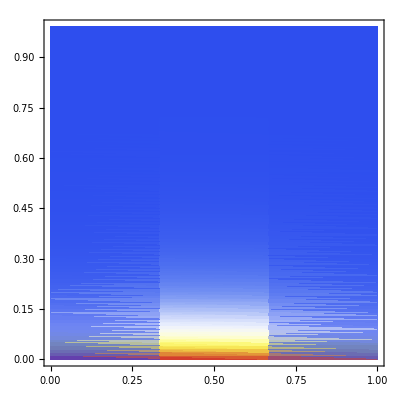

```mathematica
ListDensityPlot[data,ColorFunction->"TemperatureMap",PlotRange->All]
```

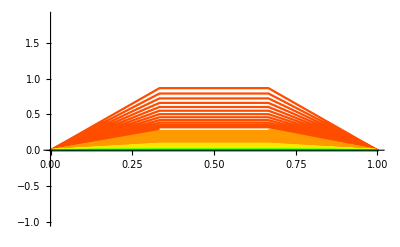

```mathematica
Show[Table[ListLinePlot[dataXtemp[[i]],PlotRange->{{0,1},{TempMin-1,TempMax+1}},PlotStyle->{Hue[(2i)/(5*Length@dataTime)]}],{i,1,Length@dataTime}]]
```

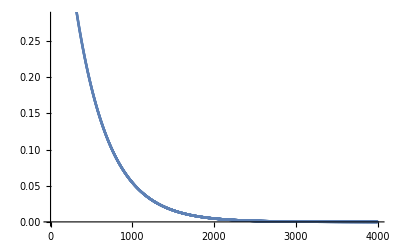

```mathematica
ListPlot[sumenergy]
```

#### Порядок аппроксимации

```mathematica
F[x_,t_]:=If[x≤t*c,(σ*c*κ^-1(c*t-x))^(1/σ),0];
G[x_,t_]:=Sin[π*x]*Exp[-π^2 t];
```

```mathematica
MaxNorm[numsol_,realsol_]:=Module[{},
Return[Max[Table[Max[numsol[[i]]-realsol[[i]]],{i,1,Length@realsol}]]];
];
NormS[numsol_,func_,t_,m_,h_]:=Module[{sol,n = Length@(numsol[[1]])},
sol=Table[Table[G[i*h,j*t],{i,0,n-1}],{j,0,m }];
Return[Max[Table[MaxNorm[numsol[[i]],sol[[i]]],{i,1,Length@numsol}]]];
];
NormLOL[sol_,G_]:=Max[Table[Abs[sol[[i,3]]-G[sol[[i,1]],sol[[i,2]]]],{i,1,Length@sol}]];
```

```mathematica
OrderTau[d1_,d2_,d3_,q_]:=Module[{f3,f2,f1,Num=10},
f1=d1[[4*Num ,3]];
f2=d2[[2*Num ,3]];
f3=d3[[Num,3]];
Return[(1/Log[q])Log[(f3-f2)/(f2-f1)]];
];
OrderH[d1_,d2_,d3_,q_]:=Module[{f3,f2,f1,Num=4},
f1 = d1[[10,4*Num]];
f2=d2[[10,2*Num]];
f3=d3[[10,Num]];
Return[(1/Log[q])Log[(f3-f2)/(f2-f1)]];
];
```

### Таблица

```mathematica
data1x1t = Import["solution_1x1t.dat"];
data1x2t  = Import["solution_1x2t.dat"];
data1x3t  = Import["solution_1x3t.dat"];
data2x1t  = Import["solution_2x1t.dat"];
data2x2t  = Import["solution_2x2t.dat"];
data2x3t  = Import["solution_2x3t.dat"];
data3x1t  = Import["solution_3x1t.dat"];
data3x2t  = Import["solution_3x2t.dat"];
data3x3t  = Import["solution_3x3t.dat"];
```

```mathematica
A={{NormLOL[data1x1t,G],NormLOL[data2x1t,G],NormLOL[data3x1t,G]},
{NormLOL[data1x2t,G],NormLOL[data2x2t,G],NormLOL[data3x2t,G]},
{NormLOL[data1x3t,G],NormLOL[data2x3t,G],NormLOL[data3x3t,G]}};
A//MatrixForm
```

(0.030784 | 0.00776328 | 0.00313051
0.03009 | 0.00689871 | 0.00223601
0.0297312 | 0.00646672 | 0.00178855)

```mathematica
howmuch=3;
n = 4; m = 1000;
```

```mathematica
H = {1/n, 1/(2n),1/(4n)};
TAU ={1/m, 1/(2m),1/(4m)};
HtauGrid=Table[Table[0,{i,1,howmuch+1}],{j,1,howmuch+1}];
For[i =2,i ≤ Length@HtauGrid,++i, 
HtauGrid[[i,1]]=H[[i-1]]//N;
For[j =2,j ≤ Length@HtauGrid,++j,
HtauGrid[[1,j]]=TAU[[j-1]]//N;
HtauGrid[[i,j]]=A[[j-1,i-1]];
];
];
HtauGrid[[1,1]]="h \\\ τ";
Grid[HtauGrid,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
```

h \ τ | 0.001 | 0.0005 | 0.00025
0.25 | 0.030784 | 0.03009 | 0.0297312
0.125 | 0.00776328 | 0.00689871 | 0.00646672
0.0625 | 0.00313051 | 0.00223601 | 0.00178855